```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
Directory[]
```

/Users/Pedro/Dropbox/Morel/mu_cases/mu_cases_0.01

```mathematica
μtotal = {};
ilist = {"20","22","24","26","28","30","32","34","36","38","40"};
jlist = {"1","2","3","4"};
For[i=0,i<11,i++;
localμ = {};
For[j=0,j<4,j++;
{iloc,jloc} = {ilist⟦i⟧,jlist⟦j⟧};
μi = Import["mu" <> jloc <> iloc <> ".txt", "Table"];
AppendTo[localμ, μi]];
AppendTo[μtotal,localμ]];
```

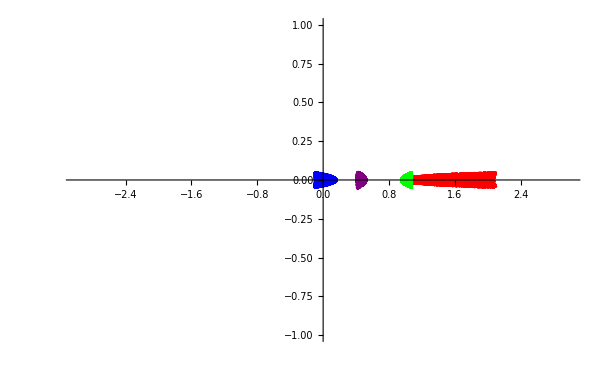

```mathematica
Show[ListPlot[μtotal⟦1,1⟧, PlotStyle->Blue], ListPlot[μtotal⟦1,2⟧, PlotStyle->Red],ListPlot[μtotal⟦1,3⟧, PlotStyle->Green],ListPlot[μtotal⟦1,4⟧, PlotStyle->Purple],PlotRange-> {{-3,3},{-1,1}}]
```

```mathematica
step =   10^-5;
```

```mathematica
maxlist1 = {};
listmean1= {};
For[i=0,i< Length[μtotal],i++;
statμi = μtotal⟦i,1,All,1⟧;
xlist = HistogramList[statμi, {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi, {0,1,step}]⟦2⟧;
AppendTo[maxlist1,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean1,Mean[statμi]]];
```

```mathematica
maxlist2 = {};
listmean2 = {};
For[i=0,i< Length[μtotal],i++;
statμi = μtotal⟦i,2,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[maxlist2,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean2,Mean[statμi]]];
```

```mathematica
maxlist3 = {};
listmean3 = {};
For[i=0,i< Length[μtotal],i++;
statμi = μtotal⟦i,3,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[maxlist3,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean3,Mean[statμi]]];
```

```mathematica
maxlist4 = {};
listmean4 = {};
For[i=0,i< Length[μtotal],i++;
statμi = μtotal⟦i,4,All,1⟧;
xlist = HistogramList[statμi,  {0,1,step}]⟦1⟧;
peaklist = HistogramList[statμi,  {0,1,step}]⟦2⟧;
AppendTo[maxlist4,xlist⟦Flatten[Position[peaklist,Max[peaklist]]]⟦1⟧⟧];
AppendTo[listmean4,Mean[statμi]]];
```

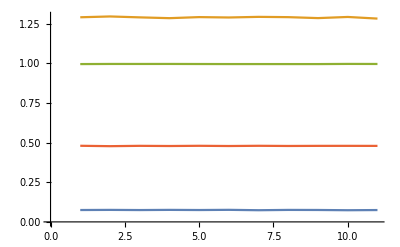

```mathematica
ListPlot[{listmean1,listmean2, listmean3, listmean4},Joined->True]
```

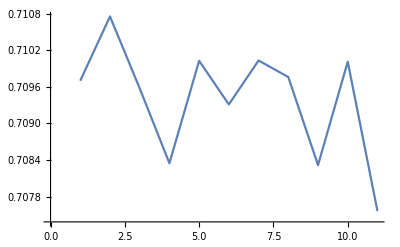

```mathematica
ListPlot[Total[{listmean1,listmean2, listmean3, listmean4}]/4,Joined->True]
```

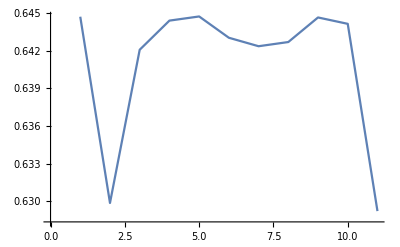

```mathematica
ListPlot[Total[{maxlist1,maxlist2, maxlist3, maxlist4}]/4,Joined->True]
```

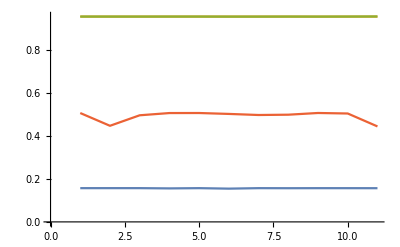

```mathematica
ListPlot[{maxlist1,maxlist2, maxlist3, maxlist4},Joined->True]
```

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-